```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
Module[{headImg,bodyImg,params,width,R,overlap},
params={width->.5,R->(.788)/2,overlap->.03};
headImg=-Graphics-;
getHead[x0_,θ_]:=Module[{base,scale,transformed,repaired},
base=Show[headImg];
scale=(width/.params)/(PlotRange/.Options[base])[[1,2]] ;

transformed=MapAt[GeometricTransformation[#,TranslationTransform[{x0,0}].RotationTransform[-θ].TranslationTransform[{-width/2,R-overlap}].ScalingTransform[{scale,scale}]]&,base,1];

repaired=Show[transformed,{PlotRange->Automatic, ImageSize->Automatic}];
repaired/.params
];

bodyImg=-Graphics-;
getBody[x0_,_]:=Module[{ψ,base,scale,transformed,repaired},
ψ=x0/R;
base=Show[bodyImg];
scale=(2R/.params)/(PlotRange/.Options[base])[[1,2]] ;

transformed=MapAt[GeometricTransformation[#,TranslationTransform[{x0,0}].RotationTransform[-ψ].TranslationTransform[{-R,-R}].ScalingTransform[{scale,scale}]]&,base,1];

repaired=Show[transformed,{PlotRange->Automatic, ImageSize->Automatic}];
repaired/.params
];

getBB8[x0_,θ_]:=Module[{},Show[{getBody[x0,θ],getHead[x0,θ]},{PlotRange->{{-10,10},{-10,10}},Axes->{True,False},AxesOrigin->{0,-R}}]/.params
];

testAnimateBB8[]:=Module[{},Animate[Evaluate@getBB8[x,th],{x,0,5},{th,-2,2},RefreshRate->60]]
]
```

```mathematica
Show[getBB8[0,0],Frame->True]
```

-Graphics-

```mathematica
testAnimateBB8[]
```

## Scratch work

```mathematica
base=Show[headImg];
```

```mathematica
Show[base,{Axes->True}]
Options[base]
```

-Graphics-

{ImageSize→{253,191},PlotRange→{{0,253},{0,191}}}

```mathematica
Show[base,Red]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,RGBColor[1, 0, 0]]

```mathematica
headImg
```

-Graphics-

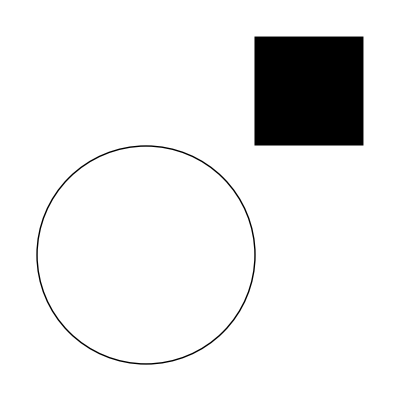

```mathematica
vit=Graphics[{Circle[],Rectangle[{1,1}]},{ImageSize->Tiny}]
```

```mathematica
|
```

```mathematica
rot=Rotate[vit,-1];
Show[Graphics@rot,{ImageSize->Tiny}]
```

-Graphics-

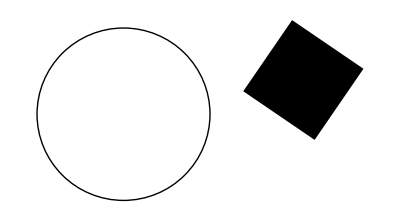

```mathematica
trans=MapAt[GeometricTransformation[#,TranslationTransform[{1,1}].RotationTransform[-.6]]&,vit,1]
```

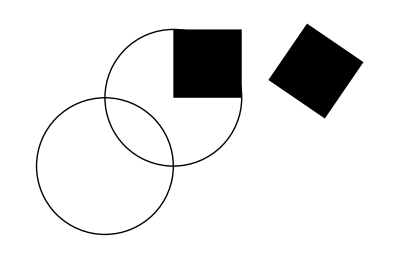

Graphics[{{Circle[{0, 0}], Rectangle[{1, 1}]}, GeometricTransformation[
   {Circle[{0, 0}], Rectangle[{1, 1}]}, {{{0.8253356149096783, 0.5646424733950354}, 
    {-0.5646424733950354, 0.8253356149096783}}, {1., 1.}}]}, {ImageSize -> Tiny}]

```mathematica
merge=Show[{vit,trans}]
merge//InputForm
```